```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
<<TheDiractionary`
dict = RandomSample[Import["CSW21.txt", "List"]];
wordsByLength = GroupBy[dict, StringLength];
```

## Version 1: 7 Letter Scrabble-gorithm

### Run Algorithm

```mathematica
RunVersion1Scrabblegorithm[1]
```

Attempt 1

Bingos Found: {INTORTS}

Tiles Left: 93 AAAAAAAAABBCCDDDDEEEEEEEEEEEEFFGGGHHIIIIIIIIJKLLLLMMNNNNNOOOOOOOPPQRRRRRSSSTTTTUUUUVVWWXYYZ??

Bingos Found: {INTORTS,ALUMINA}

Tiles Left: 86 AAAAAAABBCCDDDDEEEEEEEEEEEEFFGGGHHIIIIIIIJKLLLMNNNNOOOOOOOPPQRRRRRSSSTTTTUUUVVWWXYYZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES}

Tiles Left: 79 AAAAAAABBCCDDDEEEEEEEEEEEFFGGGHIIIIIIJKLLLMNNNNOOOOOOPPQRRRRRSSTTTTUUUVVWWYYZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS}

Tiles Left: 72 AAAAAAABBCDDDEEEEEEEEEEEFFGGGIIIIJKLLMNNNNOOOOOOPPQRRRRRSTTTUUUVVWWYYZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER}

Tiles Left: 65 AAAAAAABBCDDEEEEEEEEEEFFGGGIIIIJKLLMNNNNOOOOOQRRRSTTTUUUVVWWYYZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE}

Tiles Left: 58 AAAAAABBDDEEEEEEEEEFFGGGIIILLMNNNNOOOOOQRRRTTTUUUVVWWYYZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY}

Tiles Left: 51 AAAAAABBDEEEEEEEEEFFGGGILMNNNNOOOOORRRTTTUUVVWWYZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY,ENGINER}

Tiles Left: 44 AAAAAABBDEEEEEEEFFGGLMNNOOOOORRTTTUUVVWWYZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY,ENGINER,NYLONED}

Tiles Left: 37 AAAAAABBEEEEEEFFGGMOOOORRTTTUUVVWWZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY,ENGINER,NYLONED,AUTOMAT}

Tiles Left: 30 AAAABBEEEEEEFFGGOOORRTUVVWWZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY,ENGINER,NYLONED,AUTOMAT,AUFGABE}

Tiles Left: 23 AABEEEEEFGOOORRTVVWWZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY,ENGINER,NYLONED,AUTOMAT,AUFGABE,BERGERE}

Tiles Left: 16 AAEEFOOOTVVWWZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY,ENGINER,NYLONED,AUTOMAT,AUFGABE,BERGERE,TOWAWAY}

Tiles Left: 9 EEFOOVVZ?

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY,ENGINER,NYLONED,AUTOMAT,AUFGABE,BERGERE,TOWAWAY,FOVEOLE}

Tiles Left: 2 VZ

Success!

No Valid Words

```mathematica
dataV1=CloudGet["V.1-WordMaster"];
```

```mathematica
Dataset[dataV1]
```

### Visualize

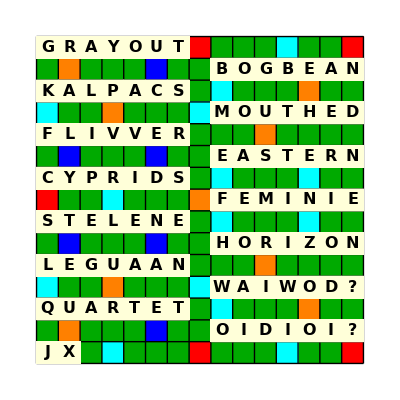

```mathematica
VisualizeVersion1[#]&/@RandomSample[dataV1,1]
```

## Version 2: 8 Letter Scrabble-gorithm

Use 2 blanks on move 14 if none required in move 13?

### Run Algorithm

```mathematica
RunVersion2Scrabblegorithm[1]
```

Bingos: {SUNBURN}

Tiles Left: 93 AAAAAAAAABCCDDDDEEEEEEEEEEEEFFGGGHHIIIIIIIIIJKLLLLMMNNNNOOOOOOOOPPQRRRRRSSSTTTTTTUUVVWWXYYZ??

Tiles Used: 7 BNNRSUU

SULPHITE played through: U

Bingos: {SUNBURN,SULPHITE}

Tiles Left: 86 AAAAAAAAABCCDDDDEEEEEEEEEEEFFGGGHIIIIIIIIJKLLLMMNNNNOOOOOOOOPQRRRRRSSTTTTTUUVVWWXYYZ??

Tiles Used: 14 BEHILNNPRSSTUU

RETINUES played through: U

Bingos: {SUNBURN,SULPHITE,RETINUES}

Tiles Left: 79 AAAAAAAAABCCDDDDEEEEEEEEEFFGGGHIIIIIIIJKLLLMMNNNOOOOOOOOPQRRRRSTTTTUUVVWWXYYZ??

Tiles Used: 21 BEEEHIILNNNPRRSSSTTUU

ANATEXES played through: T

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES}

Tiles Left: 72 AAAAAAABCCDDDDEEEEEEEFFGGGHIIIIIIIJKLLLMMNNOOOOOOOOPQRRRRTTTTUUVVWWYYZ??

Tiles Used: 28 AABEEEEEHIILNNNNPRRSSSSTTUUX

RIVETTED played through: T

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED}

Tiles Left: 65 AAAAAAABCCDDDEEEEEFFGGGHIIIIIIJKLLLMMNNOOOOOOOOPQRRRTTTUUVWWYYZ??

Tiles Used: 35 AABDEEEEEEEHIIILNNNNPRRRSSSSTTTUUVX

JAPINGLY played through: A

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY}

Tiles Left: 58 AAAAAAABCCDDDEEEEEFFGGHIIIIIKLLMMNOOOOOOOOQRRRTTTUUVWWYZ??

Tiles Used: 42 AABDEEEEEEEGHIIIIJLLNNNNNPPRRRSSSSTTTUUVXY

DEBONAIR played through: N

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY,DEBONAIR}

Tiles Left: 51 AAAAAACCDDEEEEFFGGHIIIIKLLMMNOOOOOOOQRRTTTUUVWWYZ??

Tiles Used: 49 AAABBDDEEEEEEEEGHIIIIIJLLNNNNNOPPRRRRSSSSTTTUUVXY

GRECISED played through: S

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY,DEBONAIR,GRECISED}

Tiles Left: 44 AAAAAACDEEFFGHIIIKLLMMNOOOOOOOQRTTTUUVWWYZ??

Tiles Used: 56 AAABBCDDDEEEEEEEEEEGGHIIIIIIJLLNNNNNOPPRRRRRSSSSTTTUUVXY

KAUMATUA played through: U

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY,DEBONAIR,GRECISED,KAUMATUA}

Tiles Left: 37 AAACDEEFFGHIIILLMNOOOOOOOQRTTUVWWYZ??

Tiles Used: 63 AAAAAABBCDDDEEEEEEEEEEGGHIIIIIIJKLLMNNNNNOPPRRRRRSSSSTTTTUUUVXY

TETANOID played through: T

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY,DEBONAIR,GRECISED,KAUMATUA,TETANOID}

Tiles Left: 30 AACEFFGHIILLMOOOOOOQRTUVWWYZ??

Tiles Used: 70 AAAAAAABBCDDDDEEEEEEEEEEEGGHIIIIIIIJKLLMNNNNNNOOPPRRRRRSSSSTTTTTUUUVXY

LEGALIST played through: S

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY,DEBONAIR,GRECISED,KAUMATUA,TETANOID,LEGALIST}

Tiles Left: 23 ACFFHIMOOOOOOQRUVWWYZ??

Tiles Used: 77 AAAAAAAABBCDDDDEEEEEEEEEEEEGGGHIIIIIIIIJKLLLLMNNNNNNOOPPRRRRRSSSSTTTTTTUUUVXY

VORACITY played through: T

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY,DEBONAIR,GRECISED,KAUMATUA,TETANOID,LEGALIST,VORACITY}

Tiles Left: 16 FFHMOOOOOQUWWZ??

Tiles Used: 84 AAAAAAAAABBCCDDDDEEEEEEEEEEEEGGGHIIIIIIIIIJKLLLLMNNNNNNOOOPPRRRRRRSSSSTTTTTTUUUVVXYY

WOODRUFF played through: R with a blank D

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY,DEBONAIR,GRECISED,KAUMATUA,TETANOID,LEGALIST,VORACITY,WOODRUFF}

Tiles Left: 9 HMOOOQWZ?

Tiles Used: 91 AAAAAAAAABBCCDDDDEEEEEEEEEEEEFFGGGHIIIIIIIIIJKLLLLMNNNNNNOOOOOPPRRRRRRSSSSTTTTTTUUUUVVWXYY?

```mathematica
dataV2=CloudGet["V.2-WordMaster"];
```

```mathematica
Dataset[RandomSample[CloudGet["V.2-WordMaster"],5]]
```

```mathematica
Dataset[dataV2]
```

### Visualize

```mathematica
data=RandomChoice[dataV2]
```

<|Bingos→{TINCHEL,TONETTES,EKISTICS,ANIMATES,WEENIEST,DEVELOPE,HALLOWER,PRANDIAL,OVERNAME,GUARDDOG,BOOBYISH,JANIZARY,FURFUROL,QUADDING},Overlaps→{T,E,I,S,E,H,L,A,D,S,N,R,D},Blanks→{L,N},Tiles Remaining→{I,X}|>

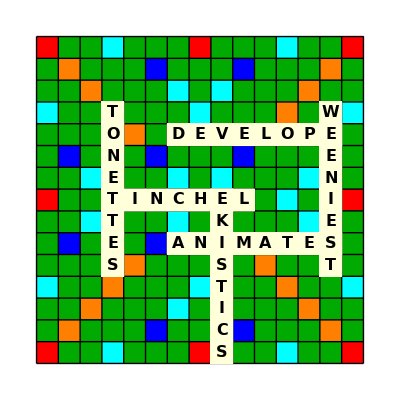

```mathematica
VisualizeVersion2[game_]:=Module[{epilog,board=CreateInitialScrabbleBoard[],bingos=game["Bingos"]},(*Place Bingos on board.*)
epilog=UpdateScrabbleBoard[bingos[[1]],{"H",4},"Right",{}];
epilog=UpdateScrabbleBoard[bingos[[2]],{"D",4},"Down",epilog];
epilog=UpdateScrabbleBoard[bingos[[3]],{"H",9},"Down",epilog];
epilog=UpdateScrabbleBoard[bingos[[4]],{"J",7},"Right",epilog];
epilog=UpdateScrabbleBoard[bingos[[5]],{"D",14},"Down",epilog];
epilog=UpdateScrabbleBoard[bingos[[6]],{"E",7},"Right",epilog];
Show[board,ImageSize->400,Epilog->epilog]
]

VisualizeVersion2[data]
```

## Version 3: Actual Scrabble Game

```mathematica
(* Initialize. *)
board=CreateInitialScrabbleBoard[]; (* Create Graphic of Empty Scrabble Board. *)
assoc=<||>;
remainingCounts=tiles[[All,"Quantity"]]; (* Initial Tiles Remaining. *)
usedCounts=AssociationThread[Keys[tiles],Table[0,27]]; (* Initially Zero Tiles have been used. *)

While[Length[assoc]==0,
Module[{next=False},
(* Turn 1. *)
pos=RandomChoice[Table[{"H",col},{col,2,8,1}]]; (* Random Position in Row H. *)
word=RandomChoice[wordsByLength[7]];
If[UpdateRemainingTileCount[remainingCounts,word,0]===tiles[[All,"Quantity"]], (* Starting 7-letter word must not require blanks. *)
Print[word, ": Choose another Starter"];
Abort[]];

Module[{boardTurn1},
   boardTurn1=
    Row[
{
DynamicModule[
{currentBoard=board,localEpilogState},
localEpilogState=UpdateScrabbleBoard[word,pos, "Right",{}];
Column[{
	Show[currentBoard,ImageSize->300,Epilog->localEpilogState],
	Button[
		"Select",
		AppendTo[assoc,Length[assoc]+1-><|"Bingo"->word,"Position"->pos,"Direction"->"Right"|>];
		remainingCounts = remainingCounts=UpdateRemainingTileCount[remainingCounts,word,0];
		usedCounts=UpdateUsedTileCount[usedCounts,word];
		epilogState=localEpilogState;
		next=True;(* Flag is set to True when selected *)
		Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];
		Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]];
		NotebookDelete[EvaluationCell[]]
		]
	}]
	],
Button["Skip",next=True;NotebookDelete[EvaluationCell[]]]}
];
If[next==False,Print[boardTurn1]];
WaitUntil[next===True];
next=False;
   ]
]
]

i=1;
While[Length[assoc]<12,
Module[{next=False},(* Initialize flag. *)
  word=wordsByLength[8][[i]]; 
  If[Length[assoc]<12,b=0,b=1];
  overlapTileOptions= Intersection[Characters[word],Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]];
  If[overlapTileOptions==={},Print[word," Has No Overlaps!"]; next=True];

Map[ (* Check the remaining counts for each overlap option. *)
If[
UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{#}]],b]==remainingCounts,
overlapTileOptions=DeleteCases[overlapTileOptions,#] (* Keep only options that can be formed with the available tiles. *)
]&,overlapTileOptions
];
If[overlapTileOptions==={},next=True];
overlapVectors=FindPossibleOverlapPositions[assoc,word,overlapTileOptions];
possibleEpilogs=AssociationMap[UpdateScrabbleBoard[word,#[[1]],#[[2]],epilogState]&,overlapVectors];
If[overlapVectors==={}, next=True];
  
  Module[{boardOptions},
   boardOptions=
    Row[
Join[
Table[
      DynamicModule[
{currentBoard=board,localEpilogState,dIdx=idx},
localEpilogState=possibleEpilogs[overlapVectors[[idx]]];
Column[{
	Show[currentBoard,ImageSize->300,Epilog->Dynamic[localEpilogState]],
	Button[
		"Select",
		AppendTo[assoc,Length[assoc]+1-><|"Bingo"->word,"Position"->overlapVectors[[dIdx]][[1]],"Direction"->overlapVectors[[dIdx]][[2]],"Overlap"->overlapVectors[[dIdx]][[3]]|>];
		remainingCounts = UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],b];
		usedCounts=UpdateUsedTileCount[usedCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]]];
		epilogState=localEpilogState;
		next=True;(* Flag is set to True when selected *)
		Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];
		Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]];
		NotebookDelete[EvaluationCell[]]
		]
	}]
	],
{idx,Length[overlapVectors]}],
{If[overlapTileOptions=!={},Button["Skip",next=True;NotebookDelete[EvaluationCell[]]],Nothing]}
]
];
If[next==False,Print[boardOptions]];
WaitUntil[next===True];
next=False;
   ];
  ];
i++; If[i>Length[wordsByLength[8]],Abort[]];If[Mod[i,10000]==0,Print["Bingos Tried: ",i]]
]
```

Tiles Used: 7 ACGHIRS

Tiles Left: 93 AAAAAAAABBCDDDDEEEEEEEEEEEEFFGGHIIIIIIIIJKLLLLMMNNNNNNOOOOOOOOPPQRRRRRSSSTTTTTTUUUUVVWWXYYZ??

TENEMENT Has No Overlaps!

Tiles Used: 14 AACDDEGHIILRRS

Tiles Left: 86 AAAAAAABBCDDEEEEEEEEEEEFFGGHIIIIIIIJKLLLMMNNNNNNOOOOOOOOPPQRRRRSSSTTTTTTUUUUVVWWXYYZ??

Tiles Used: 21 AAACDDEGHIILLOOPRRRRS

Tiles Left: 79 AAAAAABBCDDEEEEEEEEEEEFFGGHIIIIIIIJKLLMMNNNNNNOOOOOOPQRRSSSTTTTTTUUUUVVWWXYYZ??

Tiles Used: 28 AAACCDDDEGHIIIILLOOPRRRRRSTY

Tiles Left: 72 AAAAAABBDEEEEEEEEEEEFFGGHIIIIIJKLLMMNNNNNNOOOOOOPQRSSSTTTTTUUUUVVWWXYZ??

Tiles Used: 35 AAAAACCDDDDEEGHIIIILLMNOOPRRRRRSSTY

Tiles Left: 65 AAAABBEEEEEEEEEEFFGGHIIIIIJKLLMNNNNNOOOOOOPQRSSTTTTTUUUUVVWWXYZ??

Tiles Used: 42 AAAAAAAACCDDDDEEEGHIIIILLMNOOPPRRRRRSSSTTY

Tiles Left: 58 ABBEEEEEEEEEFFGGHIIIIIJKLLMNNNNNOOOOOOQRSTTTTUUUUVVWWXYZ??

Tiles Used: 49 AAAAAAAACCDDDDEEEEEGHIIIILLMNNOOOPPRRRRRRSSSSTTUY

Tiles Left: 51 ABBEEEEEEEFFGGHIIIIIJKLLMNNNNOOOOOQTTTTUUUVVWWXYZ??

Tiles Used: 56 AAAAAAAAACCDDDDEEEEEEFGHIIIILLLMNNOOOOOPPRRRRRRSSSSTTUVY

Tiles Left: 44 BBEEEEEEFGGHIIIIIJKLMNNNNOOOQTTTTUUUVWWXYZ??

Tiles Used: 63 AAAAAAAAACCDDDDEEEEEEFFGGHHIIIIILLLMNNOOOOOPPRRRRRRSSSSTTTTUUVY

Tiles Left: 37 BBEEEEEEGIIIIJKLMNNNNOOOQTTUUVWWXYZ??

Tiles Used: 70 AAAAAAAAACCDDDDEEEEEEFFGGHHIIIIIIILLLMMNNNNOOOOOOOPPRRRRRRSSSSTTTTUUVY

Tiles Left: 30 BBEEEEEEGIIJKLNNOQTTUUVWWXYZ??

Tiles Used: 77 AAAAAAAAABCCDDDDEEEEEEEFFGGHHIIIIIIIIKLLLLMMNNNNNOOOOOOOPPRRRRRRSSSSTTTTUUVYY

Tiles Left: 23 BEEEEEGIJNOQTTUUVWWXZ??

Tiles Used: 84 AAAAAAAAABBCCDDDDEEEEEEEEEFFGGHHIIIIIIIIIKLLLLMMNNNNNOOOOOOOOPPRRRRRRSSSSTTTTTUUVVYY

Tiles Left: 16 EEEGJNQTUUWWXZ??

## Twelve Words!!

```mathematica
assoc=<|1-><|"Bingo"->"DEEDFUL","Position"->{"H",2},"Direction"->"Right"|>,2-><|"Bingo"->"DECENTER","Position"->{"H",2},"Direction"->"Down","Overlap"->"D"|>,3-><|"Bingo"->"STRIDDLE","Position"->{"A",3},"Direction"->"Down","Overlap"->"E"|>,4-><|"Bingo"->"KILOMOLE","Position"->{"B",8},"Direction"->"Down","Overlap"->"L"|>,5-><|"Bingo"->"EMIGREES","Position"->{"H",4},"Direction"->"Down","Overlap"->"E"|>,6-><|"Bingo"->"CHORIOID","Position"->{"A",5},"Direction"->"Down","Overlap"->"D"|>,7-><|"Bingo"->"AMNIOTES","Position"->{"F",7},"Direction"->"Right","Overlap"->"M"|>,8-><|"Bingo"->"PIANINOS","Position"->{"E",10},"Direction"->"Down","Overlap"->"I"|>,9-><|"Bingo"->"IRRIGATE","Position"->{"C",8},"Direction"->"Right","Overlap"->"I"|>,10-><|"Bingo"->"QUOTIENT","Position"->{"K",8},"Direction"->"Right","Overlap"->"O"|>,11-><|"Bingo"->"BOWINGLY","Position"->{"H",12},"Direction"->"Down","Overlap"->"I"|>,12-><|"Bingo"->"AVOWABLY","Position"->{"N",6},"Direction"->"Right","Overlap"->"L"|>|>
usedCounts=<|"A"->5,"B"->2,"C"->2,"D"->4,"E"->11,"F"->1,"G"->3,"H"->1,"I"->9,"J"->0,"K"->1,"L"->4,"M"->2,"N"->6,"O"->8,"P"->1,"Q"->1,"R"->6,"S"->4,"T"->6,"U"->2,"V"->1,"W"->2,"X"->0,"Y"->2,"Z"->0,"?"->0|>
remainingCounts=<|"A"->4,"B"->0,"C"->0,"D"->0,"E"->1,"F"->1,"G"->0,"H"->1,"I"->0,"J"->1,"K"->0,"L"->0,"M"->0,"N"->0,"O"->0,"P"->1,"Q"->0,"R"->0,"S"->0,"T"->0,"U"->2,"V"->1,"W"->0,"X"->1,"Y"->0,"Z"->1,"?"->2|>
Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]]
Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]]
```

<|1→<|Bingo→DEEDFUL,Position→{H,2},Direction→Right|>,2→<|Bingo→DECENTER,Position→{H,2},Direction→Down,Overlap→D|>,3→<|Bingo→STRIDDLE,Position→{A,3},Direction→Down,Overlap→E|>,4→<|Bingo→KILOMOLE,Position→{B,8},Direction→Down,Overlap→L|>,5→<|Bingo→EMIGREES,Position→{H,4},Direction→Down,Overlap→E|>,6→<|Bingo→CHORIOID,Position→{A,5},Direction→Down,Overlap→D|>,7→<|Bingo→AMNIOTES,Position→{F,7},Direction→Right,Overlap→M|>,8→<|Bingo→PIANINOS,Position→{E,10},Direction→Down,Overlap→I|>,9→<|Bingo→IRRIGATE,Position→{C,8},Direction→Right,Overlap→I|>,10→<|Bingo→QUOTIENT,Position→{K,8},Direction→Right,Overlap→O|>,11→<|Bingo→BOWINGLY,Position→{H,12},Direction→Down,Overlap→I|>,12→<|Bingo→AVOWABLY,Position→{N,6},Direction→Right,Overlap→L|>|>

<|A→5,B→2,C→2,D→4,E→11,F→1,G→3,H→1,I→9,J→0,K→1,L→4,M→2,N→6,O→8,P→1,Q→1,R→6,S→4,T→6,U→2,V→1,W→2,X→0,Y→2,Z→0,?→0|>

<|A→4,B→0,C→0,D→0,E→1,F→1,G→0,H→1,I→0,J→1,K→0,L→0,M→0,N→0,O→0,P→1,Q→0,R→0,S→0,T→0,U→2,V→1,W→0,X→1,Y→0,Z→1,?→2|>

Tiles Used: 84 AAAAABBCCDDDDEEEEEEEEEEEFGGGHIIIIIIIIIKLLLLMMNNNNNNOOOOOOOOPQRRRRRRSSSSTTTTTTUUVWWYY

Tiles Left: 16 AAAAEFHJPUUVXZ??

I can play CHATEAUX (blank C) or PLATEAUX (blank L) through the T of QUOTIENT.

```mathematica
word="PLATEAUX"; 
If[Length[assoc]<12,b=0,b=1];
overlapTileOptions= Intersection[Characters[word],Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]
If[overlapTileOptions==={},Print[word," Has No Overlaps!"]];

Echo@Map[ (* Check the remaining counts for each overlap option. *)
Module[{newRemainingCounts = UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{#}]],b], negativeKeys, blanksUsed},
Echo@newRemainingCounts;
Echo@#;
If[
newRemainingCounts==remainingCounts,
overlapTileOptions=DeleteCases[overlapTileOptions,#] ,(* Keep only options that can be formed with the available tiles. *)

negativeKeys=Echo@Select[Keys[newRemainingCounts],newRemainingCounts[#]<0&];
If[negativeKeys=!={},blanksUsed=First[negativeKeys]];
Echo@blanksUsed;
]
]&,
overlapTileOptions
];

overlapVectors=Echo@FindPossibleOverlapPositions[assoc,word,overlapTileOptions];
possibleEpilogs=AssociationMap[UpdateScrabbleBoard[word,#[[1]],#[[2]],epilogState]&,overlapVectors];
```

{A,E,L,P,T,U}

<|A→4,B→0,C→0,D→0,E→1,F→1,G→0,H→1,I→0,J→1,K→0,L→0,M→0,N→0,O→0,P→1,Q→0,R→0,S→0,T→0,U→2,V→1,W→0,X→1,Y→0,Z→1,?→2|>

A

<|A→4,B→0,C→0,D→0,E→1,F→1,G→0,H→1,I→0,J→1,K→0,L→0,M→0,N→0,O→0,P→1,Q→0,R→0,S→0,T→0,U→2,V→1,W→0,X→1,Y→0,Z→1,?→2|>

E

<|A→2,B→0,C→0,D→0,E→0,F→1,G→0,H→1,I→0,J→1,K→0,L→0,M→0,N→0,O→0,P→0,Q→0,R→0,S→0,T→-1,U→1,V→1,W→0,X→0,Y→0,Z→1,?→1|>

L

{T}

T

<|A→4,B→0,C→0,D→0,E→1,F→1,G→0,H→1,I→0,J→1,K→0,L→0,M→0,N→0,O→0,P→1,Q→0,R→0,S→0,T→0,U→2,V→1,W→0,X→1,Y→0,Z→1,?→2|>

P

<|A→2,B→0,C→0,D→0,E→0,F→1,G→0,H→1,I→0,J→1,K→0,L→-1,M→0,N→0,O→0,P→0,Q→0,R→0,S→0,T→0,U→1,V→1,W→0,X→0,Y→0,Z→1,?→1|>

T

{L}

L

<|A→4,B→0,C→0,D→0,E→1,F→1,G→0,H→1,I→0,J→1,K→0,L→0,M→0,N→0,O→0,P→1,Q→0,R→0,S→0,T→0,U→2,V→1,W→0,X→1,Y→0,Z→1,?→2|>

U

{{E,L,P,T,U},{L,P,T,U},Null,{L,T,U},Null,{L,T}}

{{{H,15},Down,T}}

## Debug - Correct Options Found?

To do:
If a word has already been played to the right, words played down through it must be allowed to overlap with the tiles above and below it without penalty.

If a word has already been played down, words played to the right through it must be allowed to overlap with the tiles right and left of it without penalty.

Now, because there is no penalty for playing right through a down, or down through a right, we can get situations where a word is unaware of, and goes adjacent to, a word that it is not overlapping.

```mathematica
word="VENTANAS"
assoc = <|1-><|"Bingo"->"BROSIER","Position"->{"H",2},"Direction"->"Right"|>,2-><|"Bingo"->"LEYLANDI","Position"->{"A",6},"Direction"->"Down","Overlap"->"I"|>,3-><|"Bingo"->"OMIKRONS","Position"->{"H",4},"Direction"->"Down","Overlap"->"O"|>,4-><|"Bingo"->"NIZAMATE","Position"->{"N",4},"Direction"->"Right","Overlap"->"N"|>,5-><|"Bingo"->"ENGRAVER","Position"->{"A",3},"Direction"->"Down","Overlap"->"R"|>|>
usedCounts=<|"A"->4,"B"->1,"C"->0,"D"->1,"E"->4,"F"->0,"G"->1,"H"->0,"I"->3,"J"->0,"K"->1,"L"->2,"M"->2,"N"->4,"O"->2,"P"->0,"Q"->0,"R"->4,"S"->2,"T"->1,"U"->0,"V"->1,"W"->0,"X"->0,"Y"->1,"Z"->1,"?"->0|>
remainingCounts=<|"A"->5,"B"->1,"C"->2,"D"->3,"E"->8,"F"->2,"G"->2,"H"->2,"I"->6,"J"->1,"K"->0,"L"->2,"M"->0,"N"->2,"O"->6,"P"->2,"Q"->1,"R"->2,"S"->2,"T"->5,"U"->4,"V"->1,"W"->2,"X"->1,"Y"->1,"Z"->0,"?"->2|>
```

VENTANAS

<|1→<|Bingo→BROSIER,Position→{H,2},Direction→Right|>,2→<|Bingo→LEYLANDI,Position→{A,6},Direction→Down,Overlap→I|>,3→<|Bingo→OMIKRONS,Position→{H,4},Direction→Down,Overlap→O|>,4→<|Bingo→NIZAMATE,Position→{N,4},Direction→Right,Overlap→N|>,5→<|Bingo→ENGRAVER,Position→{A,3},Direction→Down,Overlap→R|>|>

<|A→4,B→1,C→0,D→1,E→4,F→0,G→1,H→0,I→3,J→0,K→1,L→2,M→2,N→4,O→2,P→0,Q→0,R→4,S→2,T→1,U→0,V→1,W→0,X→0,Y→1,Z→1,?→0|>

<|A→5,B→1,C→2,D→3,E→8,F→2,G→2,H→2,I→6,J→1,K→0,L→2,M→0,N→2,O→6,P→2,Q→1,R→2,S→2,T→5,U→4,V→1,W→2,X→1,Y→1,Z→0,?→2|>

```mathematica
overlapTileOptions= Intersection[Characters[word],Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]
  If[overlapTileOptions==={},Print[word," Has No Overlaps!"]]
Map[ (* Check the remaining counts for each overlap option. *)
If[
UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{#}]],0]==remainingCounts,
overlapTileOptions=DeleteCases[overlapTileOptions,#] (* Keep only options that can be formed with the available tiles. *)
]&,overlapTileOptions
];
If[overlapTileOptions==={},Print["No Valid Plays"];];
overlapVectors=FindPossibleOverlapPositions[assoc,word,overlapTileOptions]
```

{A,E,N,S,T,V}

{{{B,5},Right,E},{{F,4},Right,N}}

## Visualize End Result

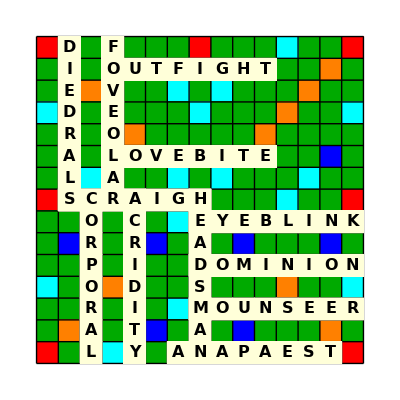

```mathematica
board=CreateInitialScrabbleBoard[];
Show[board,Epilog->epilogState]
```

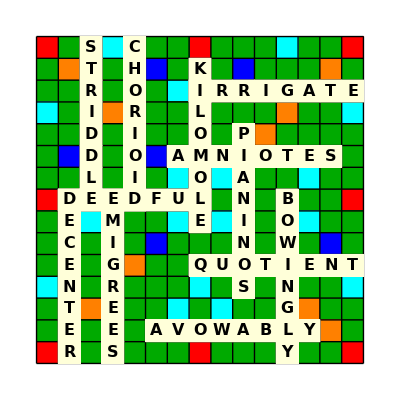

```mathematica
board=CreateInitialScrabbleBoard[];
Show[board,Epilog->epilogState]
```

```mathematica
Dataset[assoc]
```

## Finding Words when Necessary

```mathematica
dict=RandomSample[Import["CSW21.txt","List"]];
wordsByLength=GroupBy[dict,StringLength];
```

```mathematica
Select[wordsByLength[7],First[Characters[#]]=="C"&&Last[Characters[#]]=="G"&]
```

{CYCLING,CHOWING,CUCKING,CHARING,CURDING,CUTTING,CATLING,COMPING,CHIVING,CREWING,CAUMING,CRATING,CURLING,CALVING,CAPPING,CELLING,COONDOG,CANNING,CONNING,CUMMING,CHIMING,CUBBING,CRANNOG,CADGING,CHAWING,CULLING,COINING,CLAYING,CYMLING,CLEPING,CHAFING,CURBING,CARTING,CLIPING,CUFFING,CHIDING,CHINING,CEASING,CRINING,COUPING,COPPING,CEILING,CERNING,CRANING,CODLING,COILING,CHUTING,CABBING,COLTING,CHASING,CASTING,CANTDOG,CENSING,COAMING,CAMPONG,CROWING,CRAPING,COIFING,CARLING,CABLING,COSHING,CLOWING,CAUSING,COOPING,COZYING,CLOKING,COLLING,CONKING,CACHING,CUPPING,COATING,CHEFING,CACKING,CESSING,CURVING,CIELING,CAMMING,CHINWAG,CANTING,CLONING,CODDING,COURING,COSTING,CUSSING,COOKING,CASHING,CATELOG,CATTING,CARKING,COMBING,CLYPING,CATJANG,CALLING,CRIMING,COWKING,COBBING,COALING,CASKING,CORKING,COOMING,CHEWING,CRAZING,CLAWING,CURSING,COFFING,CHACING,CURRING,CONLANG,COAXING,CRAKING,COWLING,CROMING,CALKING,COTTING,CLEWING,CHOKING,CISSING,COPYING,CLOSING,COSYING,CARPING,COCKING,CREPING,CUNNING,CHUSING,CALMING,CAMPING,CEAZING,COGGING,COPSING,CLUEING,CARVING,CHORING,COWPING,CORDING,CULMING,CARDING,CRAVING,CLOYING,CORNING,CATALOG,CREEING,COOLING}

## Prove it is Solvable

```mathematica
blocks=Table[
  StringJoin[Table[" ",If[num==1,7,8]]],
  {num,1,14}
];
BingoIndex[pos_,num_,dir_,epilogState_] :=
Module[{ x=(pos[[2]]-1),y=15-(LetterNumber[pos[[1]]]-1)},
Append[epilogState,Text[Column[{Style[ToString[num],12,Bold],Style[ToString[dir],12,Bold]},Center,0],{x+0.5,y-0.5}]]
]
board=CreateInitialScrabbleBoard[];
```

```mathematica
epilog={};
epilog=UpdateScrabbleBoard[blocks[[1]], {"H",2}, "Right",epilog];
epilog=BingoIndex[{"H",2},1,"→",epilog];
turns[1]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[2]], {"A",3}, "Down",epilog];
epilog=BingoIndex[{"A",3},2,"↓",epilog];
turns[2]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[3]], {"A",5}, "Down",epilog];
epilog=BingoIndex[{"A",5},3,"↓",epilog];
turns[3]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[4]], {"A",8}, "Down",epilog];
epilog=BingoIndex[{"A",8},4,"↓",epilog];
turns[4]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[5]], {"A",7}, "Right",epilog];
epilog=BingoIndex[{"A",7},5,"→",epilog];
turns[5]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[6]], {"C",7}, "Right",epilog];
epilog=BingoIndex[{"C",7},6,"→",epilog];
turns[6]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[7]], {"E",7}, "Right",epilog];
epilog=BingoIndex[{"E",7},7,"→",epilog];
turns[7]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[8]], {"E",10}, "Down",epilog];
epilog=BingoIndex[{"E",10},8,"↓",epilog];
turns[8]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[9]], {"J",8}, "Right",epilog];
epilog=BingoIndex[{"J",8},9,"→",epilog];
turns[9]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[10]], {"H",13}, "Down",epilog];
epilog=BingoIndex[{"H",13},10,"↓",epilog];
turns[10]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[11]], {"H",15}, "Down",epilog];
epilog=BingoIndex[{"H",15},11,"↓",epilog];
turns[11]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[12]], {"H",2}, "Down",epilog];
epilog=BingoIndex[{"I",2},12,"↓",epilog];
turns[12]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[13]], {"H",4}, "Down",epilog];
epilog=BingoIndex[{"H",4},13,"↓",epilog];
turns[13]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[14]], {"N",4}, "Right",epilog];
epilog=BingoIndex[{"N",4},14,"→",epilog];
turns[14]=Show[board,Epilog->epilog];
```

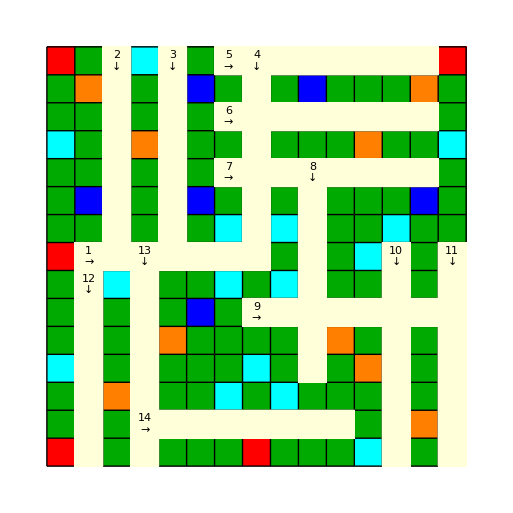

```mathematica
Show[board,Epilog->epilog]
```

```mathematica
(*Animate[turns[i],{i,1,14,1}]*)
```

## Testing

```mathematica
DynamicModule[{value=1,i=1,iteration=1,maxIterations=5},
  Dynamic[
    If[iteration<=maxIterations,
      Row[{
        Button["Click Me",
          (value=value*2;
           iteration++;
          )
        ],
        "Iteration: ",iteration, " Value: ",value
      }],
      "All iterations completed"
    ]
  ],
  Initialization:>(value=1;i=1;iteration=1)
]
```